```mathematica
Solve[(x^2+y^2)/(rs+a^2)+z^2/rs==1,rs]//FullSimplify
```

{{rs→1/2 (-a^2+x^2+y^2+z^2-√(4 a^2 z^2+(-a^2+x^2+y^2+z^2)^2))},{rs→1/2 (-a^2+x^2+y^2+z^2+√(4 a^2 z^2+(-a^2+x^2+y^2+z^2)^2))}}

```mathematica
FullSimplify[(-1+2M*r^3/(r^4+a^2*z^2))//.r->√(1/2 (-a^2+x^2+y^2+z^2+√(4 a^2 z^2+(-a^2+x^2+y^2+z^2)^2)))]
```

-1+(√2 M √(-a^2+x^2+y^2+z^2+√(4 a^2 z^2+(-a^2+x^2+y^2+z^2)^2)))/(√(4 a^2 z^2+(-a^2+x^2+y^2+z^2)^2))

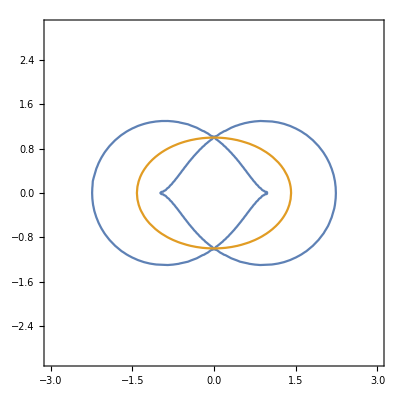

```mathematica
ClearAll[a,M,x,y,z];
M=1;
a=1;
y=0;

ContourPlot[
{
(-1+(√2 M √(-a^2+x^2+y^2+z^2+√(4 a^2 z^2+(-a^2+x^2+y^2+z^2)^2)))/(√(4 a^2 z^2+(-a^2+x^2+y^2+z^2)^2)))==0,
(√(1/2 (-a^2+x^2+y^2+z^2+√(4 a^2 z^2+(-a^2+x^2+y^2+z^2)^2))))==M+√(-a^2+M^2)},

{x,-3,3},
{z,-3,3}
]

ClearAll[a,M,x,y,z];
```

```mathematica
FortranForm[FullSimplify[√(4 a^2 z^2+(-a^2+x^2+y^2+z^2)^2)]]
```

Sqrt(4*a**2*z**2 + (-a**2 + x**2 + y**2 + z**2)**2)